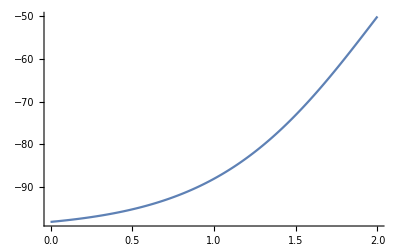

```mathematica
Subscript[m, N]=940;ℏc=197.327;
V0=100;R=2;a=0.5;μ=8/9 Subscript[m, N];
rmax=2;dr=0.01;
rlist=Range[0,rmax,dr];
len=Length[rlist];
V[r_]:=-V0/(1+Exp[(r-R)/a]);
Vmat=DiagonalMatrix[V[rlist]];
ListLinePlot[V[rlist],DataRange->{0,rmax}]
```

```mathematica
(*calculate Hamiltonian matrix and eigensystem*)
one[n_,d_]:=
DiagonalMatrix[1+0Range[n-Abs[d]],d];
H0=Vmat+-ℏc^2/(2 μ) 1/dr^2(one[len,-1]-2 one[len,0]+one[len,1]);
k[En_]:=Sqrt[-(2μ En)/ℏc^2];
B[En_]:=1-dr k[En];
Hnew[En_]:=(H=H0;H[[len,len]]=Vmat[[len,len]]+-ℏc^2/(2 μ) 1/dr^2(-2+B[En]);H)
eigenv[{En_,i_}]:=({eval,evec}=Eigensystem[Hnew[En]];{eval[[-i]],i})
```

```mathematica
n=1;En=NestWhileList[eigenv,{-V0/2,n},Abs[#1[[1]]-#2[[1]]]>0.00000001&,2,10][[-1,1]]
```

-46.4875

```mathematica
{eval,evec}={eval,evec}[[All,Position[{eval,evec}[[1,All]],_?(#<0&)][[All,1]]]];
```

```mathematica
(*En=NestWhileList[SetPrecision[eigenv,5]{-V0,1},UnsameQ,2,100]*)
(*FindRoot[eigenv[{x,1}][[1]]==x,{x,-V0/2,-V0,0},WorkingPrecision->2]*)
(*Plot[{eigenv[{x,n}][[1]],#&[x]},{x,-V0,0}]*)
```

```mathematica
wave[En_,r_]:=Exp[-k[En] r];
const[i_]:=evec[[i,-1]]/wave[eval[[i]],rmax];
rmaxx=10.;
Manipulate[ListLinePlot[{Transpose[{rlist,evec⟦i⟧}],Transpose[{Range[rmax,rmaxx,dr],const[i] wave[eval[[i]],Range[rmax,rmaxx,dr]]}]},PlotRange->All],{i,1,Length[eval],1}]
```

Part::partd: Part specification evec⟦1⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {rlist,evec⟦1⟧} cannot be transposed.

Range::range: Range specification in Range[rmax,rmaxx,dr] does not have appropriate bounds.

Part::partd: Part specification eval⟦1⟧ is longer than depth of object.

Range::range: Range specification in Range[rmax,rmaxx,dr] does not have appropriate bounds.

Transpose::nmtx: The first two levels of {Range[rmax,rmaxx,dr],const[1] wave[eval⟦1⟧,Range[rmax,rmaxx,dr]]} cannot be transposed.

Transpose::nmtx: The first two levels of {Range[rmax,rmaxx,dr],const[1.] wave[eval⟦1⟧,Range[rmax,rmaxx,dr]]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.